```mathematica
ClearAll["Global`*"]
```

```mathematica
vv:=3
t[n_,a_]:= (-1)^(Floor[n/a]-Floor[(n-1)/a])

et[n_,k_]:=et[n,k]=Sum[et[j,k-1] et[n/j,1],{j,Divisors[n]}];et[n_,1]:=t[n,vv];et[n_,0]:=0;et[1,0]:=1
et2[n_,k_]:=et2[n,k]=Sum[(-1)^j Binomial[k,j] et[n,k-j],{j,0,k}]
ET2[n_,k_] := ET2[n,k]=Sum[ et2[j,k],{j,2,n}]
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[vv,n]}]
lin[n_]:=Sum[(-1)^(k+1)/k et2[n,k],{k,1,Log[2,n]}]
Lin[n_]:=Sum[(-1)^(k+1)/k ET2[n,k],{k,1,Log[2,n]}]+LAdd[n]
Lin2[n_]:=Sum[(-1)^(k+1)/k ET2[n,k],{k,1,Log[2,n]}]
```

```mathematica
Lin[100]
```

428/15

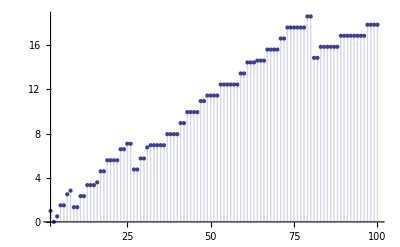

```mathematica
DiscretePlot[ Lin2[n],{n,2,100}]
```

```mathematica
Table[ {n,lin[n]},{n,2,40}]//TableForm
```

2 | 1
3 | 1
4 | -3/2
5 | 1
6 | 0
7 | -1
8 | 7/3
9 | 1/2
10 | 0
11 | -1
12 | 2
13 | 1
14 | 0
15 | 0
16 | -7/4
17 | 1
18 | -2
19 | 1
20 | 2
21 | 0
22 | 2
23 | 1
24 | -2
25 | -3/2
26 | 0
27 | 1/3
28 | -2
29 | 1
30 | 0
31 | 1
32 | 11/5
33 | 2
34 | 0
35 | 0
36 | 2
37 | 1
38 | 0
39 | -2
40 | -2